```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
Print["Runs in the list: ",runNum={12681,12684,12687,12688,12689,12690,12691,12692}];(*11159,11369*)
Print["Size: ",runn=Dimensions[runNum][[1]]];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Runs in the list: {12681,12684,12687,12688,12689,12690,12691,12692}

Size: 8

```mathematica
metadata1=Table[{},{k,1,Round[runn/2]}];
metadata2=Table[0,{k,1,Round[runn/2]}];
ftdatud=Table[{},{k,1,Round[runn/2]}];
ptdatud=Table[0,{k,1,Round[runn/2]}];
fit1=Table[0,{k,1,Round[runn/2]}];
ftdatudmon=Table[{},{k,1,Round[runn/2]}];
ptdatudmon=Table[0,{k,1,Round[runn/2]}];
fit2=Table[0,{k,1,Round[runn/2]}];
For[i=1,i≤Round[runn/2],i++,
Print["Starting with Run # : ",runNum[[(2i)-1]]," & ",runNum[[(2i)]]];
metadata1[[i]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[(2i)-1]],10,6],"\\",IntegerString[runNum[[(2i)-1]],10,6],"_Meta3.edm"],metaStructure2];
metadata2[[i]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[(2i)]],10,6],"\\",IntegerString[runNum[[(2i)]],10,6],"_Meta3.edm"],metaStructure2];
maxCy=metadata1[[i]][[-1]][[2]];
(*UD*)
Print["Fit1:UD"];
tab=Table[{55+(k-1)*25,{(metadata1[[i]][[k]][[27]]+metadata1[[i]][[k]][[28]])/1000,(Sqrt[metadata1[[i]][[k]][[27]]+metadata1[[i]][[k]][[28]]])/1000}},{k,1,maxCy}];
ptdatud[[i]]=AppendTo[tab,{380,{(metadata2[[i]][[1]][[27]]+metadata2[[i]][[1]][[28]])/1000,(Sqrt[metadata2[[i]][[1]][[27]]+metadata2[[i]][[1]][[28]]])/1000}}];
If[i==2,ptdatud[[i]]=Delete[ptdatud[[i]],4]];
If[i==3,ptdatud[[i]]=Delete[ptdatud[[i]],3]];
ftdatud[[i]]=Transpose[{ptdatud[[i]][[;;,1]],ptdatud[[i]][[;;,2]][[;;,1]]}];
Print[fit1[[i]]=NonlinearModelFit[ftdatud[[i]],(bb Exp[cc t]+dd Exp[ee t]+aa),{{aa,1},{bb,10},{cc,-.1},{dd,10},{ee,-.1}},t,Method->NMinimize]];
(*UD/Mon*)
Print["Fit2:UD/Mon"];
tab2=Table[{55+(k-1)*25,{(metadata1[[i]][[k]][[27]]+metadata1[[i]][[k]][[28]])/metadata1[[i]][[k]][[30]],(Sqrt[metadata1[[i]][[k]][[27]]]+Sqrt[metadata1[[i]][[k]][[28]]])/metadata1[[i]][[k]][[30]]}},{k,1,maxCy}];
ptdatudmon[[i]]=AppendTo[tab2,{380,{(metadata2[[i]][[1]][[27]]+metadata2[[i]][[1]][[28]])/metadata2[[i]][[1]][[30]],(Sqrt[metadata2[[i]][[1]][[27]]]+Sqrt[metadata2[[i]][[1]][[28]]])/metadata2[[i]][[1]][[30]]}}];
If[i==2,ptdatudmon[[i]]=Delete[ptdatudmon[[i]],4]];
If[i==3,ptdatudmon[[i]]=Delete[ptdatudmon[[i]],3]];
ftdatudmon[[i]]=Transpose[{ptdatudmon[[i]][[;;,1]],ptdatudmon[[i]][[;;,2]][[;;,1]]}];
Print[fit2[[i]]=NonlinearModelFit[ftdatudmon[[i]],(bb Exp[cc t]+dd Exp[ee t]+aa),{{aa,1},{bb,10},{cc,-.1},{dd,10},{ee,-.1}},t,Method->NMinimize]];
Print["---"];
];
(*
{aa,bb,cc,dd,ee};
{{aa,1},{bb,1},{cc,-1},{dd,1},{ee,-1}}
*)
```

Starting with Run # : 12681 & 12684

Fit1:UD

FittedModel[1.32355+173.412 ⅇ^(-1.03538 t)+16.4029 ⅇ^(-0.00603346 t)]

Fit2:UD/Mon

FittedModel[0.00622475+27.65 ⅇ^(-0.697654 t)+0.0759593 ⅇ^(-0.00619004 t)]

---

Starting with Run # : 12687 & 12688

Fit1:UD

FittedModel[10.8416-13.6656 ⅇ^(-2.15553 t)+91.8044 ⅇ^(-0.0105479 t)]

Fit2:UD/Mon

FittedModel[0.00972756-6.17056 ⅇ^(-0.497426 t)+0.0960547 ⅇ^(-0.00758587 t)]

---

Starting with Run # : 12689 & 12690

Fit1:UD

FittedModel[7.26364+28.4414 ⅇ^(-4.65532 t)+79.8589 ⅇ^(-0.00729495 t)]

Fit2:UD/Mon

FittedModel[0.00840625+29.5281 ⅇ^(-1.33283 t)+0.0894173 ⅇ^(-0.00657063 t)]

---

Starting with Run # : 12691 & 12692

Fit1:UD

FittedModel[5.0024+517.598 ⅇ^(-1.42655 t)+72.3616 ⅇ^(-0.0061986 t)]

Fit2:UD/Mon

FittedModel[0.0122227+6.07127 ⅇ^(-1.01924 t)+0.0957033 ⅇ^(-0.0082354 t)]

---

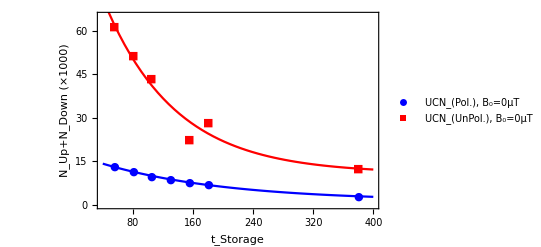

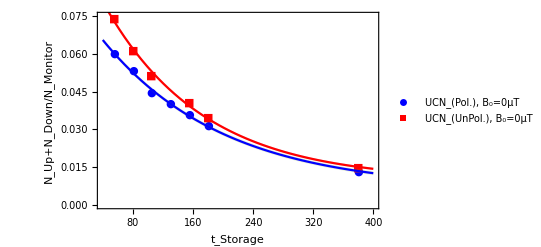

```mathematica
Show[{
EDAListPlot[ptdatud[[1]],ptdatud[[2]],PlotLegends->{"UCN_(Pol.), B_0=0μT","UCN_(UnPol.), B_0=0μT"},PlotRange->{{40,400},{0,65}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down (×1000)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit1[[1]][t],fit1[[2]][t],fit1[[1]][t]+ptdatud[[1]][[1]][[2]][[2]],fit1[[1]][t]-ptdatud[[1]][[1]][[2]][[2]],fit1[[2]][t]+ptdatud[[2]][[1]][[2]][[2]],fit1[[2]][t]-ptdatud[[2]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
Show[{
EDAListPlot[ptdatudmon[[1]],ptdatudmon[[2]],PlotLegends->{"UCN_(Pol.), B_0=0μT","UCN_(UnPol.), B_0=0μT"},PlotRange->{{40,400},{0,0.075}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit2[[1]][t],fit2[[2]][t],fit2[[1]][t]+ptdatudmon[[1]][[1]][[2]][[2]],fit2[[1]][t]-ptdatudmon[[1]][[1]][[2]][[2]],fit2[[2]][t]+ptdatudmon[[2]][[1]][[2]][[2]],fit2[[2]][t]-ptdatudmon[[2]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

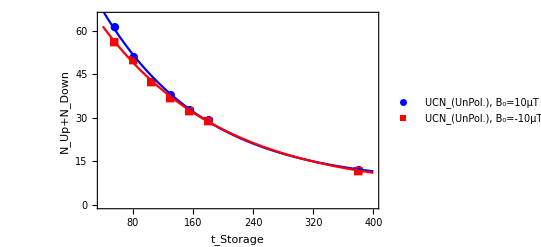

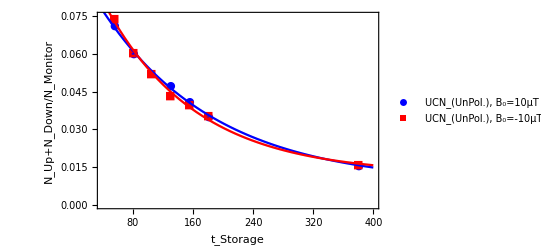

```mathematica
Show[{
EDAListPlot[ptdatud[[3]],ptdatud[[4]],PlotLegends->{"UCN_(UnPol.), B_0=10μT","UCN_(UnPol.), B_0=-10μT"},PlotRange->{{40,400},{0,65}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit1[[3]][t],fit1[[4]][t],fit1[[3]][t]+ptdatud[[3]][[1]][[2]][[2]],fit1[[3]][t]-ptdatud[[3]][[1]][[2]][[2]],fit1[[4]][t]+ptdatud[[4]][[1]][[2]][[2]],fit1[[4]][t]-ptdatud[[4]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
Show[{
EDAListPlot[ptdatudmon[[3]],ptdatudmon[[4]],PlotLegends->{"UCN_(UnPol.), B_0=10μT","UCN_(UnPol.), B_0=-10μT"},PlotRange->{{40,400},{0,0.075}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit2[[3]][t],fit2[[4]][t],fit2[[3]][t]+ptdatudmon[[3]][[1]][[2]][[2]],fit2[[3]][t]-ptdatudmon[[3]][[1]][[2]][[2]],fit2[[4]][t]+ptdatudmon[[4]][[1]][[2]][[2]],fit2[[4]][t]-ptdatudmon[[4]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

```mathematica
ptdatudmon[[2]]
ptdatudmon[[3]]
ptdatudmon[[4]]
```

{{55,{0.0739628,0.000422606}},{80,{0.0614265,0.000383263}},{105,{0.051403,0.000349193}},{155,{0.0406109,0.000381609}},{180,{0.0346558,0.00029071}},{380,{0.014797,0.000186751}}}

{{55,{0.0712409,0.000406908}},{80,{0.0600757,0.000376268}},{130,{0.0474324,0.000343512}},{155,{0.0411074,0.000320581}},{180,{0.035053,0.000289089}},{380,{0.015804,0.000203152}}}

{{55,{0.0741104,0.000442673}},{80,{0.0606785,0.00038343}},{105,{0.0520993,0.000357561}},{130,{0.0435714,0.000321261}},{155,{0.0398941,0.000312909}},{180,{0.0353641,0.000292852}},{380,{0.015945,0.000207199}}}

```mathematica
superdat={};
superdat=AppendTo[superdat,{ptdatudmon[[2]][[1]][[1]],Mean[{PlusMinus[ptdatudmon[[2]][[1]][[2]][[1]],ptdatudmon[[2]][[1]][[2]][[2]]],PlusMinus[ptdatudmon[[3]][[1]][[2]][[1]],ptdatudmon[[3]][[1]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[1]][[2]][[1]],ptdatudmon[[4]][[1]][[2]][[2]]]}]}];
superdat=AppendTo[superdat,{ptdatudmon[[2]][[2]][[1]],Mean[{PlusMinus[ptdatudmon[[2]][[2]][[2]][[1]],ptdatudmon[[2]][[2]][[2]][[2]]],PlusMinus[ptdatudmon[[3]][[2]][[2]][[1]],ptdatudmon[[3]][[2]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[2]][[2]][[1]],ptdatudmon[[4]][[2]][[2]][[2]]]}]}];
superdat=AppendTo[superdat,{ptdatudmon[[2]][[3]][[1]],Mean[{PlusMinus[ptdatudmon[[2]][[3]][[2]][[1]],ptdatudmon[[2]][[3]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[3]][[2]][[1]],ptdatudmon[[4]][[3]][[2]][[2]]]}]}];
superdat=AppendTo[superdat,{ptdatudmon[[3]][[3]][[1]],Mean[{PlusMinus[ptdatudmon[[3]][[3]][[2]][[1]],ptdatudmon[[3]][[3]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[4]][[2]][[1]],ptdatudmon[[4]][[4]][[2]][[2]]]}]}];
superdat=AppendTo[superdat,{ptdatudmon[[2]][[4]][[1]],Mean[{PlusMinus[ptdatudmon[[2]][[4]][[2]][[1]],ptdatudmon[[2]][[4]][[2]][[2]]],PlusMinus[ptdatudmon[[3]][[4]][[2]][[1]],ptdatudmon[[3]][[4]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[5]][[2]][[1]],ptdatudmon[[4]][[5]][[2]][[2]]]}]}];
AccountingForm[TableForm[SetPrecision[superdat,10]]]
descdat=ReadList[StringJoin[descDir,"\\","desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
Print["Runs in the list: ",runNum2=descdat[[;;,4]]];
Print["Storage time in the list: ",ts2=descdat[[;;,7]]];
Print["Size: ",runn2=Dimensions[runNum2][[1]]];
For[runi=1,runi≤runn2,runi++,
metadatascr=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum2[[runi]],10,6],"\\",IntegerString[runNum2[[runi]],10,6],"_Meta5.edm"],metaStructure2];
superdat=AppendTo[superdat,{ts2[[runi]],Mean[Table[(PlusMinus[(metadatascr[[k]][[27]]+metadatascr[[k]][[28]]),Sqrt[(metadatascr[[k]][[27]]+metadatascr[[k]][[28]])]])/PlusMinus[(metadatascr[[k]][[30]]),Sqrt[(metadatascr[[k]][[30]])]],{k,1,Dimensions[metadatascr][[1]]}]]}];
];
superdat=Sort[superdat,#1[[1]]<#2[[1]]&];
expsuperdat=AccountingForm[TableForm[SetPrecision[superdat,10]]]
```

55.00000000 | 0.07310000000±0.0002500000000
80.00000000 | 0.06073000000±0.0002200000000
105.0000000 | 0.05175000000±0.0002500000000
130.0000000 | 0.04550000000±0.0002300000000
155.0000000 | 0.04054000000±0.0002000000000

Runs in the list: {12693,12695,12697,12704,12707,12770,12771,12772,12773,12774,12775,12778,12779,12780,12781}

Storage time in the list: {180,180,180,380,380,200,220,240,260,280,300,320,340,360,300}

Size: 15

55.00000000 | 0.07310000000±0.0002500000000
80.00000000 | 0.06073000000±0.0002200000000
105.0000000 | 0.05175000000±0.0002500000000
130.0000000 | 0.04550000000±0.0002300000000
155.0000000 | 0.04054000000±0.0002000000000
180.0000000 | 0.03496300000±0.00003900000000
180.0000000 | 0.03433600000±0.00001000000000
180.0000000 | 0.03484400000±0.00001600000000
200.0000000 | 0.03648900000±0.00003800000000
220.0000000 | 0.03341600000±0.00003900000000
240.0000000 | 0.03062900000±0.00003800000000
260.0000000 | 0.02824400000±0.00004200000000
280.0000000 | 0.02584600000±0.00004600000000
300.0000000 | 0.02281700000±0.00007400000000
300.0000000 | 0.02501800000±0.00007600000000
320.0000000 | 0.02162700000±0.00003100000000
340.0000000 | 0.01977700000±0.00003100000000
360.0000000 | 0.01894600000±0.00003100000000
380.0000000 | 0.01486900000±0.00002200000000
380.0000000 | 0.01520700000±0.00004200000000

```mathematica
superdat2={};
gaps={1,1,1,1,1,3,1,1,1,1,1,2,1,1,1,2};
Total[gaps]==Dimensions[superdat][[1]]
For[j=1,j≤Dimensions[gaps][[1]],j++,
superdat2=AppendTo[superdat2,Mean[Table[superdat[[j2]],{j2,Total[gaps[[1;;j]]]+1-gaps[[j]],Total[gaps[[1;;j]]]}]]];
];
expsuperdat2=AccountingForm[TableForm[SetPrecision[superdat2,10]]];
superdat3=superdat2+Table[{23,PlusMinus[0,.00004]},{k,1,Dimensions[superdat2][[1]]}];
expsuperdat3=AccountingForm[TableForm[SetPrecision[superdat3,10]]]
Export["expsuperdat2.dat",superdat3]
```

True

78.00000000 | 0.07310000000±0.0002500000000
103.0000000 | 0.06073000000±0.0002200000000
128.0000000 | 0.05175000000±0.0002500000000
153.0000000 | 0.04550000000±0.0002300000000
178.0000000 | 0.04054000000±0.0002000000000
203.0000000 | 0.03471400000±0.00004200000000
223.0000000 | 0.03648900000±0.00005500000000
243.0000000 | 0.03341600000±0.00005600000000
263.0000000 | 0.03062900000±0.00005500000000
283.0000000 | 0.02824400000±0.00005800000000
303.0000000 | 0.02584600000±0.00006100000000
323.0000000 | 0.02392000000±0.00006800000000
343.0000000 | 0.02162700000±0.00005100000000
363.0000000 | 0.01977700000±0.00005100000000
383.0000000 | 0.01894600000±0.00005100000000
403.0000000 | 0.01503800000±0.00004600000000

expsuperdat2.dat

FittedModel[0.00965169+0.111428 ⅇ^(-0.00740545 t)]

FittedModel[0.00516096+0.101879 ⅇ^(-0.00527396 t)]

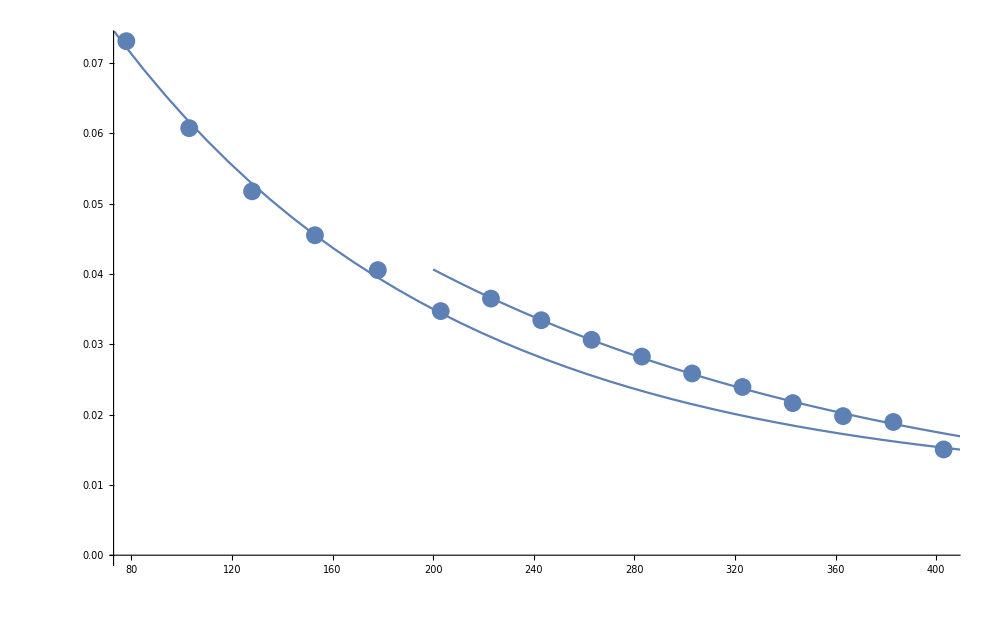

```mathematica
ptsuperdat3=Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,1,Dimensions[superdat3][[1]]}];
ftsuperdat3=Table[{superdat3[[k]][[1]],superdat3[[k]][[2]][[1]]},{k,1,Dimensions[superdat3][[1]]}];
Print[nlm0=NonlinearModelFit[Join[ftsuperdat3[[1;;6]],{ftsuperdat3[[16]]}],(bb Exp[t/cc]+aa),{{aa,1},{bb,10},{cc,-.1}},t,Method->NMinimize]]
Print[nlm01=NonlinearModelFit[ftsuperdat3[[7;;15]],(bb Exp[t/cc]+aa),{{aa,1},{bb,10},{cc,-.1}},t,Method->NMinimize]]
Show[{EDAListPlot[ptsuperdat3,ImageSize->1000],Plot[nlm0[xx],{xx,10,420}],Plot[nlm01[xx],{xx,200,420}]}]
rat[x_]:=nlm0[x]/nlm01[x];
```

{{78,{0.0731,0.00025}},{103,{0.06073,0.00022}},{128,{0.05175,0.00025}},{153,{0.0455,0.00023}},{178,{0.04054,0.0002}},{203,{0.034714,0.000042}},{223,{0.0309364,0.0000466306}},{243,{0.0280569,0.0000470189}},{263,{0.0255571,0.0000458924}},{283,{0.0235049,0.0000482682}},{303,{0.021531,0.0000508159}},{323,{0.0200193,0.0000569112}},{343,{0.0182498,0.0000430361}},{363,{0.0168849,0.000043542}},{383,{0.0164194,0.0000441988}},{403,{0.015038,0.000046}}}

{{78,0.00025},{103,0.00022},{128,0.00025},{153,0.00023},{178,0.0002},{203,0.000042},{223,0.0000466306},{243,0.0000470189},{263,0.0000458924},{283,0.0000482682},{303,0.0000508159},{323,0.0000569112},{343,0.0000430361},{363,0.000043542},{383,0.0000441988},{403,0.000046}}

FittedModel[0.00010402+0.1 ⅇ^(-10. t)]

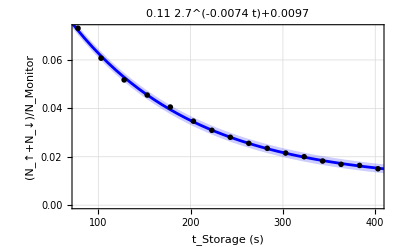

78.00 | 0.07310±0.0002500
103.0 | 0.06073±0.0002200
128.0 | 0.05175±0.0002500
153.0 | 0.04550±0.0002300
178.0 | 0.04054±0.0002000
203.0 | 0.03471±0.00004200
223.0 | 0.03094±0.00004663
243.0 | 0.02806±0.00004702
263.0 | 0.02556±0.00004589
283.0 | 0.02350±0.00004827
303.0 | 0.02153±0.00005082
323.0 | 0.02002±0.00005691
343.0 | 0.01825±0.00004304
363.0 | 0.01688±0.00004354
383.0 | 0.01642±0.00004420
403.0 | 0.01504±0.00004600

expsuperdat3.dat

```mathematica
ptseries1=Join[Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,1,6}],Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,16,16}]];
ptseries2=Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}*HeavisidePi[(superdat3[[k]][[1]]-303)/180]*rat[superdat3[[k]][[1]]]},{k,7,15}];
ftseries1=Transpose[{ptseries1[[;;,1]],ptseries1[[;;,2]][[;;,2]]}];
ftseries2=Transpose[{ptseries2[[;;,1]],ptseries2[[;;,2]][[;;,2]]}];
ptallseries=Join[ptseries1,ptseries2];
ptallseries=Sort[ptallseries,#1[[1]]<#2[[1]]&]
ftallseries=Join[ftseries1,ftseries2];
ftallseries=Sort[ftallseries,#1[[1]]<#2[[1]]&]
Print[nlm2=NonlinearModelFit[ftallseries,(bb Exp[t/cc]+aa),{{aa,0.01},{bb,.1},{cc,-.1}},t]]
Show[{
EDAListPlot[ptallseries,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel->SetPrecision[nlm0["BestFit"],2],PlotMarkers->{Red,Medium}],
Plot[{nlm0[xx],nlm0[xx]+nlm0["ParameterErrors"][[1]],nlm0[xx]-nlm0["ParameterErrors"][[1]]},{xx,10,420},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
AccountingForm[TableForm[SetPrecision[Table[{ptallseries[[k]][[1]],PlusMinus[ptallseries[[k]][[2]][[1]],ptallseries[[k]][[2]][[2]]]},{k,1,Dimensions[ptallseries][[1]]}],4]]]
Export["expsuperdat3.dat",Table[{ptallseries[[k]][[1]],PlusMinus[ptallseries[[k]][[2]][[1]],ptallseries[[k]][[2]][[2]]]},{k,1,Dimensions[ptallseries][[1]]}]]
```

```mathematica
newruns={13013,13015};
newdat={};
newts={10,40,70,100,130,160,200,230,260,290,320,350,380}+23;
Dimensions[newruns][[1]]
For[i=1,i≤Dimensions[newruns][[1]],i++,
newdat=Join[newdat,ReadList[StringJoin[ScrDir,"\\",IntegerString[newruns[[i]],10,6],"_Meta3.edm"],metaStructure2]];
];
Dimensions[newdat][[1]]
ptnewdat=Table[{newts[[k]],{2(newdat[[k]][[27]]+newdat[[k]][[28]])/newdat[[k]][[30]],(Sqrt[newdat[[k]][[27]]]+Sqrt[newdat[[k]][[28]]])/newdat[[k]][[30]]}},{k,1,Dimensions[newdat][[1]]}]
ftnewdat=Table[{newts[[k]],2(newdat[[k]][[27]]+newdat[[k]][[28]])/newdat[[k]][[30]]},{k,1,Dimensions[newdat][[1]]}]
```

2

13

{{33,{0.152285,0.000489667}},{63,{0.115681,0.000424808}},{93,{0.0926913,0.000382308}},{123,{0.0780776,0.000350415}},{153,{0.0649736,0.000319115}},{183,{0.0569987,0.000301303}},{223,{0.0458028,0.00026619}},{253,{0.0402424,0.000253251}},{283,{0.0349287,0.000232803}},{313,{0.0302981,0.000215622}},{343,{0.0280638,0.000211323}},{373,{0.0239452,0.000194427}},{403,{0.0208945,0.000179632}}}

{{33,0.152285},{63,0.115681},{93,0.0926913},{123,0.0780776},{153,0.0649736},{183,0.0569987},{223,0.0458028},{253,0.0402424},{283,0.0349287},{313,0.0302981},{343,0.0280638},{373,0.0239452},{403,0.0208945}}

FittedModel[0.0185629+0.172955 ⅇ^(-0.00861037 t)]

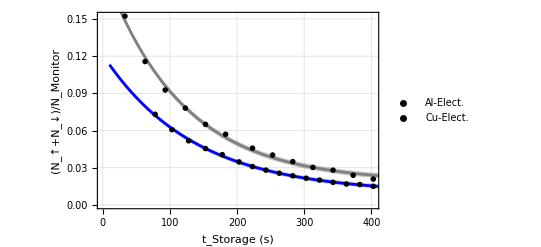

33.00 | 0.1523±0.0004897
63.00 | 0.1157±0.0004248
93.00 | 0.09269±0.0003823
123.0 | 0.07808±0.0003504
153.0 | 0.06497±0.0003191
183.0 | 0.05700±0.0003013
223.0 | 0.04580±0.0002662
253.0 | 0.04024±0.0002533
283.0 | 0.03493±0.0002328
313.0 | 0.03030±0.0002156
343.0 | 0.02806±0.0002113
373.0 | 0.02395±0.0001944
403.0 | 0.02089±0.0001796

```mathematica
Print[nlmnew=NonlinearModelFit[ftnewdat,(bb Exp[t/cc]+aa),{{aa,1},{bb,10},{cc,-.1}},t,Method->NMinimize]]
Show[{
EDAListPlot[ptallseries,ptnewdat,PlotLegends->{"Al-Elect.","Cu-Elect."},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{{Red,Medium},{Pink,Medium}}],
Plot[{nlm0[xx],nlm0[xx]+nlm0["ParameterErrors"][[1]],nlm0[xx]-nlm0["ParameterErrors"][[1]],nlmnew[xx],nlmnew[xx]+nlmnew["ParameterErrors"][[1]],nlmnew[xx]-nlmnew["ParameterErrors"][[1]]},{xx,10,420},Filling->{{2->{3}},{5->{6}}},FillingStyle->{{Opacity[.5],Blue},{Opacity[.5],Gray}},PlotStyle->{{Blue,Thickness[.005]},None,None,{Gray,Thickness[.005]},None,None}]
}]
AccountingForm[TableForm[SetPrecision[Table[{ptnewdat[[k]][[1]],PlusMinus[ptnewdat[[k]][[2]][[1]],ptnewdat[[k]][[2]][[2]]]},{k,1,Dimensions[ptnewdat][[1]]}],4]]]
```

```mathematica
Export["expsuperdat_cu3.dat",Table[{ptnewdat[[k]][[1]],PlusMinus[ptnewdat[[k]][[2]][[1]],ptnewdat[[k]][[2]][[2]]]},{k,1,Dimensions[ptnewdat][[1]]}]]
```

expsuperdat_cu3.dat